```mathematica
Interpreter["PhysicalQuantity"]["torque"]
```

Torque

```mathematica
Entity["PhysicalQuantity","Torque"]
```

torque

```mathematica
Entity["PhysicalQuantity","Torque"]["Dataset"]
```

```mathematica
Entity["PhysicalQuantity"]
```

## Coherent SI Unit

```mathematica
ResourceObject["SI Brochure Data"]
```

ResourceObject[…]

```mathematica
ResourceData[ResourceObject["SI Brochure Data"],All]
```

<|base-quantities-and-dimensions→,base-quantities-and-units→,coherent-derived-units-in-the-SI-expressed-terms-of-base-units→,coherent-derived-units-whose-names-and-symbols-include-SI-coherent-derived-units-with-special-names-and-symbols→,Dataset→,defining-constants-of-the-SI→,RawData→<|hyperfine-transition-frequency-of-Cs→<|numerical-value→9192631770,unit→Hz|>,speed-of-light-in-vacuum→<|numerical-value→299792458,unit→m s^-1|>,Planck-constant→<|numerical-value→6.62607×10^-34,unit→J s|>,elementary-charge→<|numerical-value→1.60218×10^-19,unit→C|>,Boltzmann-constant→<|numerical-value→1.38065×10^-23,unit→J K^-1|>,Avogadro-constant→<|numerical-value→6.02214×10^23,unit→mol^-1|>,luminous-efficacy→<|numerical-value→683,unit→lm W^-1|>|>,SI-prefixes→,SI-units-with-special-names-and-symbols→|>

```mathematica
ResourceData[ResourceObject["SI Brochure Data"],"coherent-derived-units-whose-names-and-symbols-include-SI-coherent-derived-units-with-special-names-and-symbols"]
```

```mathematica
PhysicalQuantity//ClearAll
PhysicalQuantity[string_]:=Entity["PhysicalQuantity",string]
```

```mathematica
PhysicalQuantity["HeatCapacity"]
```

heat capacity

```mathematica
ud=QuantityVariableDimensions["Energy"]
```

{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}}

```mathematica
pqs=ResourceFunction["PhysicalQuantityLookup"][ud,"Entity"]
```

{acoustic energy,atomic binding energy,atomic energy,binding energy,biogas energy,bond energy,elastic energy,electromagnetic energy,energy,equivalent energy,excitation energy,Fermi energy,fundamental temperature,geothermal energy,gravitational binding energy,magnetic energy,mass energy equivalent,massergy,nuclear binding energy,ponderomotive energy,reaction energy,resonance energy,seismic energy equivalent,separation energy,solar energy,surface energy,tidal energy,total energy,vibrational energy,water energy,wave energy,wind energy,zero-point energy,amount of heat,heat gain,heat loss,power spectral density,active energy,adiabatic work,alpha disintegration energy,applied moment of force,battery energy capacity,bending moment of force,beta disintegration energy,chemical energy,cogging torque,disintegration energy,elastic potential energy,electrical energy,electric apparent energy,electric potential energy,electric reactive energy,electron affinity,enthalpy,ergotropy,exhange integral,exergy,factored bending moment of force,first ionization energy,food energy,friction torque,Gibbs energy,gravitational potential energy,Hamiltonian function,Hamiltonian operator,Helmholtz energy,hysteresis torque,internal energy,ionization energy,kinetic energy,Lagrangian function,latent heat,latent heat of condensation,latent heat of fusion,latent heat of phase transition,latent heat of solidification,latent heat of vaporization,level width,load frequency shift,magnetic domain wall energy,maximum beta particle energy,mechanical energy,mechanical work,moment of force,noise spectral density,nuclear energy,particle width,photon energy,potential energy,pulsar luminosity,radiant energy,radio luminosity,relativistic kinetic energy,rotational energy,second ionization energy,sound energy,spectral radiant flux (with respect to frequency),tempergy,thermodynamic free energy,thermodynamic work,third ionization energy,torque,vacuum energy,virtual work,viscous drag torque,work,work function}

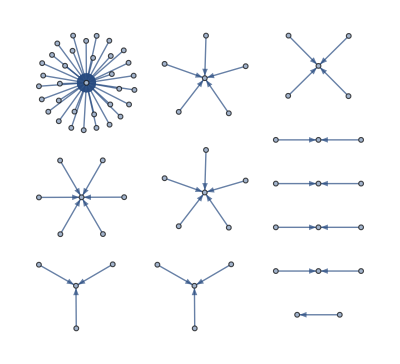

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]]
```

{{acoustic energy,energy,atomic binding energy,atomic energy,binding energy,biogas energy,bond energy,elastic energy,electromagnetic energy,equivalent energy,excitation energy,Fermi energy,fundamental temperature,geothermal energy,gravitational binding energy,magnetic energy,mass energy equivalent,massergy,nuclear binding energy,ponderomotive energy,reaction energy,resonance energy,seismic energy equivalent,separation energy,solar energy,surface energy,tidal energy,total energy,vibrational energy,water energy,wave energy,wind energy,zero-point energy,vacuum energy},{adiabatic work,work,ergotropy,exergy,mechanical work,thermodynamic work,virtual work},{latent heat of condensation,latent heat,latent heat of fusion,latent heat of phase transition,latent heat of solidification,latent heat of vaporization},{chemical energy,potential energy,elastic potential energy,electric potential energy,gravitational potential energy,nuclear energy},{cogging torque,torque,friction torque,hysteresis torque,viscous drag torque},{first ionization energy,ionization energy,second ionization energy,third ionization energy},{alpha disintegration energy,disintegration energy,beta disintegration energy,maximum beta particle energy},{relativistic kinetic energy,kinetic energy,rotational energy},{Gibbs energy,thermodynamic free energy,Helmholtz energy},{applied moment of force,bending moment of force,factored bending moment of force},{heat gain,amount of heat,heat loss},{radio luminosity,spectral radiant flux (with respect to frequency)}}

```mathematica
TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1]
```

{{radio luminosity,spectral radiant flux (with respect to frequency)}}

```mathematica
Map[#["Dataset"]&,TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1],2]
```

{{,}[Dataset]}

```mathematica
Map[#["Dataset"]&,SortBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length][[2]],1]
```

{,,}

```mathematica
Map[#["PropertyAssociation"]&,TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1],2]
```

{{<|abbreviations→Missing[NotAvailable],algebraic types→{positive real,scalar},alternate names→Missing[NotAvailable],base physical quantity→spectral radiant flux (with respect to frequency),canonical unit→1 W/Hz,classes→{physical quantity instances},dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},entity classes→{physical quantity instances},instances→Missing[NotApplicable],name→radio luminosity,named SI unit→Missing[None],physical property type→Missing[NotAvailable],quantity variable→{} RadioLuminosity,SI base unit→1 kg m^2/s^2,SI unit→1 W/Hz,standard identifiers→<||>,standard symbols→<||>,symbols→{}|>,<|abbreviations→Missing[NotAvailable],algebraic types→{positive real,scalar},alternate names→{spectral radiant power (with respect to frequency)},base physical quantity→Missing[NotAvailable],canonical unit→1 W/Hz,classes→{},dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},entity classes→{},instances→{radio luminosity},name→spectral radiant flux (with respect to frequency),named SI unit→Missing[None],physical property type→Missing[NotAvailable],quantity variable→Φ_(e,ν) SpectralRadiantFluxWithRespectToFrequency,SI base unit→1 kg m^2/s^2,SI unit→1 W/Hz,standard identifiers→<|Wikidata→Q101460704|>,standard symbols→<||>,symbols→{}|>}[PropertyAssociation]}

```mathematica
#["PropertyAssociation"]&@First@Flatten@TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1]
```

<|abbreviations→Missing[NotAvailable],algebraic types→{positive real,scalar},alternate names→Missing[NotAvailable],base physical quantity→spectral radiant flux (with respect to frequency),canonical unit→1 W/Hz,classes→{physical quantity instances},dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},entity classes→{physical quantity instances},instances→Missing[NotApplicable],name→radio luminosity,named SI unit→Missing[None],physical property type→Missing[NotAvailable],quantity variable→{} RadioLuminosity,SI base unit→1 kg m^2/s^2,SI unit→1 W/Hz,standard identifiers→<||>,standard symbols→<||>,symbols→{}|>

```mathematica
PacletInstall["PeterBurbery/DimensionalAnalysis"]
```

PacletObject[…]

```mathematica
Needs["PeterBurbery`DimensionalAnalysis`"]
```

```mathematica
CanonicalDimensionalProduct[]
```

```mathematica
TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1]
```

{{radio luminosity,spectral radiant flux (with respect to frequency)}}

```mathematica
CanonicalDimensionalProduct[Entity["PhysicalQuantity","RadioLuminosity"]]
```

T^-2L^2M^1

```mathematica
KeyMap[CanonicalName,<|EntityProperty["PhysicalQuantity","Abbreviations"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","AlgebraicTypes"]->{"positive real","scalar"},EntityProperty["PhysicalQuantity","AlternateNames"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]->Entity["PhysicalQuantity","SpectralRadiantFluxWithRespectToFrequency"],EntityProperty["PhysicalQuantity","CanonicalUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","Classes"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Dimensions"]->{{"LengthUnit",2},{"MassUnit",1},{"TimeUnit",-2}},EntityProperty["PhysicalQuantity","EntityClasses"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Instances"]->Missing["NotApplicable"],EntityProperty["PhysicalQuantity","Name"]->"radio luminosity",EntityProperty["PhysicalQuantity","NamedSIUnit"]->Missing["None"],EntityProperty["PhysicalQuantity","PhysicalPropertyType"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","QuantityVariable"]->{} "RadioLuminosity",EntityProperty["PhysicalQuantity","SIBaseUnit"]->Quantity[1, ("Kilograms" ("Meters")^2)/("Seconds")^2],EntityProperty["PhysicalQuantity","SIUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","StandardIdentifiers"]-><||>,EntityProperty["PhysicalQuantity","StandardSymbols"]-><||>,EntityProperty["PhysicalQuantity","Symbols"]->{}|>]
```

<|Abbreviations→Missing[NotAvailable],AlgebraicTypes→{positive real,scalar},AlternateNames→Missing[NotAvailable],BasePhysicalQuantity→spectral radiant flux (with respect to frequency),CanonicalUnit→1 W/Hz,Classes→{physical quantity instances},Dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},EntityClasses→{physical quantity instances},Instances→Missing[NotApplicable],Name→radio luminosity,NamedSIUnit→Missing[None],PhysicalPropertyType→Missing[NotAvailable],QuantityVariable→{} RadioLuminosity,SIBaseUnit→1 kg m^2/s^2,SIUnit→1 W/Hz,StandardIdentifiers→<||>,StandardSymbols→<||>,Symbols→{}|>

```mathematica
Join[KeyMap[CanonicalName,<|EntityProperty["PhysicalQuantity","Abbreviations"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","AlgebraicTypes"]->{"positive real","scalar"},EntityProperty["PhysicalQuantity","AlternateNames"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]->Entity["PhysicalQuantity","SpectralRadiantFluxWithRespectToFrequency"],EntityProperty["PhysicalQuantity","CanonicalUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","Classes"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Dimensions"]->{{"LengthUnit",2},{"MassUnit",1},{"TimeUnit",-2}},EntityProperty["PhysicalQuantity","EntityClasses"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Instances"]->Missing["NotApplicable"],EntityProperty["PhysicalQuantity","Name"]->"radio luminosity",EntityProperty["PhysicalQuantity","NamedSIUnit"]->Missing["None"],EntityProperty["PhysicalQuantity","PhysicalPropertyType"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","QuantityVariable"]->{} "RadioLuminosity",EntityProperty["PhysicalQuantity","SIBaseUnit"]->Quantity[1, ("Kilograms" ("Meters")^2)/("Seconds")^2],EntityProperty["PhysicalQuantity","SIUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","StandardIdentifiers"]-><||>,EntityProperty["PhysicalQuantity","StandardSymbols"]-><||>,EntityProperty["PhysicalQuantity","Symbols"]->{}|>],<|"CanonicalDimensionalProduct"->CanonicalDimensionalProduct[Entity["PhysicalQuantity","RadioLuminosity"]]|>]
```

<|Abbreviations→Missing[NotAvailable],AlgebraicTypes→{positive real,scalar},AlternateNames→Missing[NotAvailable],BasePhysicalQuantity→spectral radiant flux (with respect to frequency),CanonicalUnit→1 W/Hz,Classes→{physical quantity instances},Dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},EntityClasses→{physical quantity instances},Instances→Missing[NotApplicable],Name→radio luminosity,NamedSIUnit→Missing[None],PhysicalPropertyType→Missing[NotAvailable],QuantityVariable→{} RadioLuminosity,SIBaseUnit→1 kg m^2/s^2,SIUnit→1 W/Hz,StandardIdentifiers→<||>,StandardSymbols→<||>,Symbols→{},CanonicalDimensionalProduct→T^-2L^2M^1|>

```mathematica
Join[KeyMap[CanonicalName,<|EntityProperty["PhysicalQuantity","Abbreviations"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","AlgebraicTypes"]->{"positive real","scalar"},EntityProperty["PhysicalQuantity","AlternateNames"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]->Entity["PhysicalQuantity","SpectralRadiantFluxWithRespectToFrequency"],EntityProperty["PhysicalQuantity","CanonicalUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","Classes"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Dimensions"]->{{"LengthUnit",2},{"MassUnit",1},{"TimeUnit",-2}},EntityProperty["PhysicalQuantity","EntityClasses"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Instances"]->Missing["NotApplicable"],EntityProperty["PhysicalQuantity","Name"]->"radio luminosity",EntityProperty["PhysicalQuantity","NamedSIUnit"]->Missing["None"],EntityProperty["PhysicalQuantity","PhysicalPropertyType"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","QuantityVariable"]->{} "RadioLuminosity",EntityProperty["PhysicalQuantity","SIBaseUnit"]->Quantity[1, ("Kilograms" ("Meters")^2)/("Seconds")^2],EntityProperty["PhysicalQuantity","SIUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","StandardIdentifiers"]-><||>,EntityProperty["PhysicalQuantity","StandardSymbols"]-><||>,EntityProperty["PhysicalQuantity","Symbols"]->{}|>],<|"CanonicalDimensionalProduct"->CanonicalDimensionalProduct[Entity["PhysicalQuantity","RadioLuminosity"]]|>]//InputForm
```

<|"Abbreviations" -> Missing["NotAvailable"], 
 "AlgebraicTypes" -> {"positive real", "scalar"}, 
 "AlternateNames" -> Missing["NotAvailable"], "BasePhysicalQuantity" -> 
  Entity["PhysicalQuantity", "SpectralRadiantFluxWithRespectToFrequency"], 
 "CanonicalUnit" -> Quantity[1, "Watts"/"Hertz"], 
 "Classes" -> {EntityClass["PhysicalQuantity", "PhysicalQuantityInstance"]}, 
 "Dimensions" -> {{"LengthUnit", 2}, {"MassUnit", 1}, {"TimeUnit", -2}}, 
 "EntityClasses" -> {EntityClass["PhysicalQuantity", "PhysicalQuantityInstance"]}, 
 "Instances" -> Missing["NotApplicable"], "Name" -> "radio luminosity", 
 "NamedSIUnit" -> Missing["None"], "PhysicalPropertyType" -> 
  Missing["NotAvailable"], "QuantityVariable" -> 
  QuantityVariable[{}, "RadioLuminosity"], 
 "SIBaseUnit" -> Quantity[1, ("Kilograms"*"Meters"^2)/"Seconds"^2], 
 "SIUnit" -> Quantity[1, "Watts"/"Hertz"], "StandardIdentifiers" -> <||>, 
 "StandardSymbols" -> <||>, "Symbols" -> {}, "CanonicalDimensionalProduct" -> 
  Row[{Superscript["T", -2], Superscript["L", 2], Superscript["M", 1]}]|>

## Functions

```mathematica
PhysicalQuantityDataWithDimensionalProductAdded//ClearAll
PhysicalQuantityDataWithDimensionalProductAdded[q_Entity]:=Join[KeyMap[CanonicalName,q["PropertyAssociation"]],<|"CanonicalDimensionalProduct"->CanonicalDimensionalProduct[q]|>]
```

```mathematica
SimplifiedPhysicalQuantityDataWithDimensionalProductAdded//ClearAll
SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[q_Entity]:=Join[AssociationThread[{"Name","SIUnit","SIBaseUnit"}->Lookup[KeyMap[CanonicalName,q["PropertyAssociation"]],{"Name","SIUnit","SIBaseUnit"}]],<|"CanonicalDimensionalProduct"->CanonicalDimensionalProduct[q]|>]
```

```mathematica
PhysicalQuantityDataWithDimensionalProductAdded[Entity["PhysicalQuantity","RadioLuminosity"]]
```

<|Abbreviations→Missing[NotAvailable],AlgebraicTypes→{positive real,scalar},AlternateNames→Missing[NotAvailable],BasePhysicalQuantity→spectral radiant flux (with respect to frequency),CanonicalUnit→1 W/Hz,Classes→{physical quantity instances},Dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},EntityClasses→{physical quantity instances},Instances→Missing[NotApplicable],Name→radio luminosity,NamedSIUnit→Missing[None],PhysicalPropertyType→Missing[NotAvailable],QuantityVariable→{} RadioLuminosity,SIBaseUnit→1 kg m^2/s^2,SIUnit→1 W/Hz,StandardIdentifiers→<||>,StandardSymbols→<||>,Symbols→{},CanonicalDimensionalProduct→T^-2L^2M^1|>

```mathematica
Dataset[PhysicalQuantityDataWithDimensionalProductAdded[Entity["PhysicalQuantity","RadioLuminosity"]]]
```

```mathematica
Dataset[PhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity["QEDEulerHeisenbergLagrangianFactor"]]]
```

This is a graph.

### Function Test

```mathematica
AssociationThread[{"Name","SIUnit","SIBaseUnit"}->Lookup[KeyMap[CanonicalName,Entity["PhysicalQuantity","RadioLuminosity"]["PropertyAssociation"]],{"Name","SIUnit","SIBaseUnit"}]]
```

<|Name→radio luminosity,SIUnit→1 W/Hz,SIBaseUnit→1 kg m^2/s^2|>

## using the function

```mathematica
SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]&/@{"MassEnergyEquivalent","ElectricPotentialEnergy","FrictionTorque","Exergy"}
```

{<|Name→mass energy equivalent,SIUnit→1 J,SIBaseUnit→1 kg m^2/s^2,CanonicalDimensionalProduct→T^-2L^2M^1|>,<|Name→electric potential energy,SIUnit→1 J,SIBaseUnit→1 kg m^2/s^2,CanonicalDimensionalProduct→T^-2L^2M^1|>,<|Name→friction torque,SIUnit→1 m N,SIBaseUnit→1 kg m^2/s^2,CanonicalDimensionalProduct→T^-2L^2M^1|>,<|Name→exergy,SIUnit→1 J,SIBaseUnit→1 kg m^2/s^2,CanonicalDimensionalProduct→T^-2L^2M^1|>}

This is a graph.

```mathematica
Dataset[SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]]&/@{"MassEnergyEquivalent","ElectricPotentialEnergy","FrictionTorque","Exergy","LatentHeatOfVaporization","RotationalEnergy","SecondIonizationEnergy"}
```

{,,,,,,}

## Graph that groups by unit

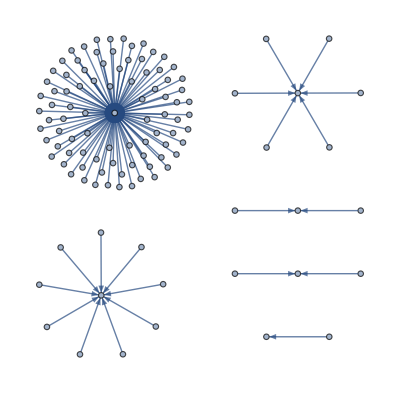

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","SIUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
Dataset[SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]]&/@{"LevelWidth","PulsarLuminosity","FrictionTorque","ElectricReactiveEnergy","PhotonEnergy","MagneticDomainWallEnergy"}
```

{,,,,,}

### Find a unique ID

```mathematica
SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]["SIUnit"]&/@{"LevelWidth","PulsarLuminosity","FrictionTorque","ElectricReactiveEnergy","PhotonEnergy","MagneticDomainWallEnergy"}
```

{1 J,1 W/Hz,1 m N,1 s A V,1 s W,1 m^4 T^2/H}

```mathematica
AssociationThread[{"LevelWidth","PulsarLuminosity","FrictionTorque","ElectricReactiveEnergy","PhotonEnergy","MagneticDomainWallEnergy"}->(SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]["SIUnit"]&/@{"LevelWidth","PulsarLuminosity","FrictionTorque","ElectricReactiveEnergy","PhotonEnergy","MagneticDomainWallEnergy"})]
```

<|LevelWidth→1 J,PulsarLuminosity→1 W/Hz,FrictionTorque→1 m N,ElectricReactiveEnergy→1 s A V,PhotonEnergy→1 s W,MagneticDomainWallEnergy→1 m^4 T^2/H|>

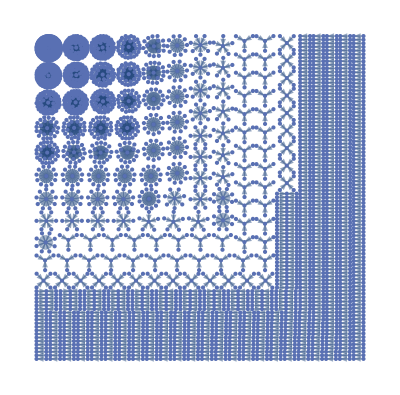

```mathematica
graphOfPhysicalQuantitiesGroupedBySIUnit=Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","SIUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
PersistResourceFunction["PhysicalQuantityData"]
```

Success[…]

```mathematica
PhysicalQuantityData[]
```

## Analyzing the graph

How many distinct units are there?

```mathematica
Length[ConnectedGraphComponents[graphOfPhysicalQuantitiesGroupedBySIUnit]]
```

3833

Compare this to the number of physical quantities.

```mathematica
Length[PhysicalQuantityData[]]
```

3046